```mathematica
(* Discretizes the Fermi Surface and calculates the conductivity integrals*)
```

```mathematica
Energy[x_,y_]:=Cos[x] - 2*Cos[y]
vx[x_,y_]:=-Sin[x]
vy[x_,y_]:=2*Sin[y]
v[x_,y_]:=Sqrt[vx[x,y]^2+vy[x,y]^2]
σxx[de_,τ_]:=τ*Module[{iso1,coor1,coor2,mesh1,mesh2,measure1,measure2,i,result=0,cc1,cc2,cc3,V},iso1=DiscretizeRegion[ImplicitRegion[Energy[x,y]==de && -3.14<=x<=3.14 && -3.14<=y<=3.14,{x,y}],MaxCellMeasure->0.0005];
coor1=MeshCoordinates[iso1];
mesh1=MeshCells[iso1,1];
measure1=AnnotationValue[{iso1,1},MeshCellMeasure];
For[i=1,i<=Length[mesh1],i++, cc1=coor1[[mesh1[[i,1,1]]]]; cc2=coor1[[mesh1[[i,1,2]]]]; 
V=(v[cc1[[1]],cc1[[2]]]+v[cc2[[1]],cc2[[2]]])/2;result=result+measure1[[i]]*vx[cc1[[1]],cc1[[2]]]^2/(Abs[V]*(2Pi)^2)];result
]
σyy[de_,τ_]:=τ*Module[{iso1,coor1,coor2,mesh1,mesh2,measure1,measure2,i,result=0,cc1,cc2,cc3,V},iso1=DiscretizeRegion[ImplicitRegion[Energy[x,y]==de && -3.14<=x<=3.14 && -3.14<=y<=3.14,{x,y}],MaxCellMeasure->0.0005];
coor1=MeshCoordinates[iso1];
mesh1=MeshCells[iso1,1];
measure1=AnnotationValue[{iso1,1},MeshCellMeasure];
For[i=1,i<=Length[mesh1],i++, cc1=coor1[[mesh1[[i,1,1]]]]; cc2=coor1[[mesh1[[i,1,2]]]]; 
V=(v[cc1[[1]],cc1[[2]]]+v[cc2[[1]],cc2[[2]]])/2;result=result+measure1[[i]]*vy[cc1[[1]],cc1[[2]]]^2/(V*(2Pi)^2)];result
]
```

```mathematica
x=Table[{de,σxx[de,1]},{de,-2.5,2.5,0.1}]
y=Table[{de,σyy[de,1]},{de,-2.5,2.5,0.1}]
```

{{-2.5,0.0518227},{-2.4,0.0609216},{-2.3,0.0695542},{-2.2,0.0776821},{-2.1,0.0852869},{-2.,0.0923497},{-1.9,0.0987519},{-1.8,0.104555},{-1.7,0.109613},{-1.6,0.113864},{-1.5,0.117202},{-1.4,0.119488},{-1.3,0.120441},{-1.2,0.119394},{-1.1,0.116338},{-1.,0.10756},{-0.9,0.098647},{-0.8,0.0940919},{-0.7,0.090706},{-0.6,0.0881963},{-0.5,0.0861763},{-0.4,0.0848562},{-0.3,0.0837425},{-0.2,0.0830938},{-0.1,0.0826739},{1.38778×10^-16,0.082539},{0.1,0.0827017},{0.2,0.0831127},{0.3,0.0838402},{0.4,0.0849783},{0.5,0.0864541},{0.6,0.0882623},{0.7,0.0909832},{0.8,0.0942236},{0.9,0.0994471},{1.,0.109258},{1.1,0.116433},{1.2,0.119337},{1.3,0.119961},{1.4,0.119175},{1.5,0.116686},{1.6,0.113165},{1.7,0.108783},{1.8,0.103604},{1.9,0.0977323},{2.,0.0912111},{2.1,0.0841259},{2.2,0.0764755},{2.3,0.0683391},{2.4,0.0597245},{2.5,0.0506474}}

{{-2.5,0.110376},{-2.4,0.132226},{-2.3,0.153952},{-2.2,0.175619},{-2.1,0.197238},{-2.,0.218747},{-1.9,0.240527},{-1.8,0.262185},{-1.7,0.28405},{-1.6,0.30604},{-1.5,0.328568},{-1.4,0.351611},{-1.3,0.375512},{-1.2,0.396699},{-1.1,0.4247},{-1.,0.46244},{-0.9,0.496752},{-0.8,0.523483},{-0.7,0.542028},{-0.6,0.557022},{-0.5,0.567497},{-0.4,0.578607},{-0.3,0.584897},{-0.2,0.590906},{-0.1,0.593922},{1.38778×10^-16,0.594869},{0.1,0.594282},{0.2,0.591014},{0.3,0.586},{0.4,0.580099},{0.5,0.570982},{0.6,0.557382},{0.7,0.544878},{0.8,0.524053},{0.9,0.504116},{1.,0.471046},{1.1,0.428808},{1.2,0.400983},{1.3,0.37577},{1.4,0.355852},{1.5,0.332764},{1.6,0.310231},{1.7,0.288029},{1.8,0.266088},{1.9,0.244264},{2.,0.222524},{2.1,0.200743},{2.2,0.178995},{2.3,0.157136},{2.4,0.135208},{2.5,0.113213}}

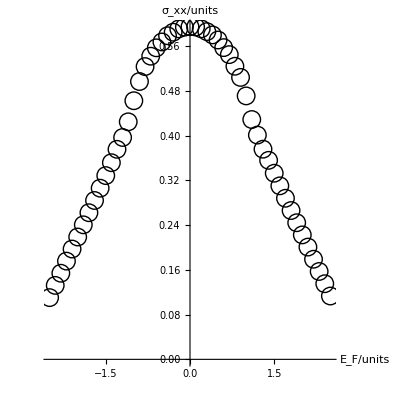

```mathematica
ListPlot[y,PlotStyle->Black,PlotMarkers->{Style["○",18]},Frame->False,Axes->True,FrameStyle->Directive[Black],FrameTicksStyle->Directive[Black,24],AspectRatio->1, AxesLabel->{"E_F/units", "σ_xx/units"}]
```

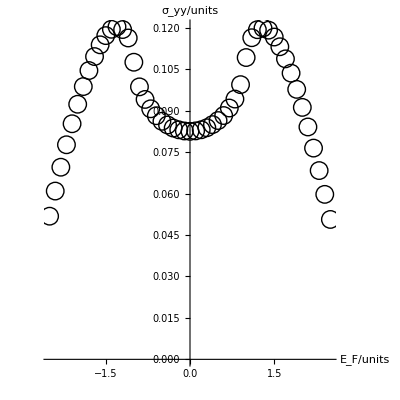

```mathematica
ListPlot[x,PlotStyle->Black,PlotMarkers->{Style["○",18]},Frame->False,Axes->True,FrameStyle->Directive[Black,Thin],FrameTicksStyle->Directive[Black,24],AspectRatio->1,AxesLabel->{"E_F/units", "σ_yy/units"}]
```